```mathematica
SetDirectory[NotebookDirectory[]];
```

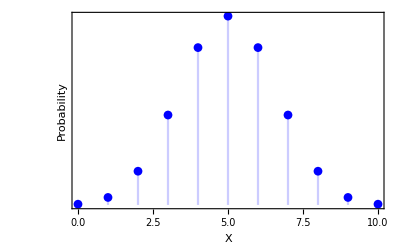

```mathematica
g=DiscretePlot[PDF[BinomialDistribution[10,0.5],x],{x,0,10},PlotStyle->Blue,Frame->{True,True,False,False},PlotMarkers->{Automatic, 9},FrameLabel->{"X","Probability"},LabelStyle->{Black,FontSize->16},FrameTicks->{True,None}]
```

```mathematica
Export["binomial.pdf",g]
```

binomial.pdf

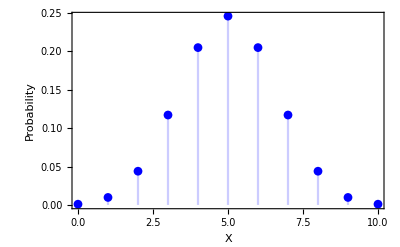

```mathematica
g=DiscretePlot[PDF[BinomialDistribution[10,0.5],x],{x,0,10},PlotStyle->Blue,Frame->{True,True,False,False},PlotMarkers->{Automatic, 9},FrameLabel->{"X","Probability"},LabelStyle->{Black,FontSize->16},FrameTicks->{True,True}]
```

```mathematica
Export["binomial_values.pdf",g]
```

binomial_values.pdf

## Many worlds

```mathematica
imagesize=400;
g2=Show[DiscretePlot[PDF[BinomialDistribution[10,0.5],x],{x,0,10},PlotStyle->Blue,Frame->{True,True,False,False},PlotMarkers->{Automatic, 9},FrameLabel->{"X","Probability"},LabelStyle->{Black,FontSize->16},FrameTicks->{True,None},
ImageSize->imagesize,PlotLabel->StringJoin["X ~ B(10,",ToString@0.5,")"]],DiscretePlot[PDF[BinomialDistribution[10,0.5],x],{x,3,3},AspectRatio->1.5,Filling->Axis,PlotStyle->{Black},FillingStyle->Directive[{Thickness[0.03],Opacity[0.6,Black]}],PlotRange->{{0,25},{0,0.2}}]];
g1=Show[DiscretePlot[PDF[BinomialDistribution[10,0.1],x],{x,0,10},PlotStyle->Orange,Frame->{True,True,False,False},PlotMarkers->{Automatic, 9},FrameLabel->{"X","Probability"},LabelStyle->{Black,FontSize->16},FrameTicks->{True,None},
ImageSize->imagesize,PlotLabel->StringJoin["X ~ B(10,",ToString@0.1,")"]],DiscretePlot[PDF[BinomialDistribution[10,0.1],x],{x,3,3},AspectRatio->1.5,Filling->Axis,PlotStyle->{Black},FillingStyle->Directive[{Thickness[0.03],Opacity[0.6,Black]}],PlotRange->{{0,25},{0,0.2}}]];
g3=Show[DiscretePlot[PDF[BinomialDistribution[10,0.8],x],{x,0,10},PlotStyle->Darker[Green],Frame->{True,True,False,False},PlotMarkers->{Automatic, 9},FrameLabel->{"X","Probability"},LabelStyle->{Black,FontSize->16},FrameTicks->{True,None},
ImageSize->imagesize,PlotLabel->StringJoin["X ~ B(10,",ToString@0.8,")"]],DiscretePlot[PDF[BinomialDistribution[10,0.8],x],{x,3,3},AspectRatio->1.5,Filling->Axis,PlotStyle->{Black},FillingStyle->Directive[{Thickness[0.03],Opacity[0.6,Black]}],PlotRange->{{0,25},{0,0.2}}]];
```

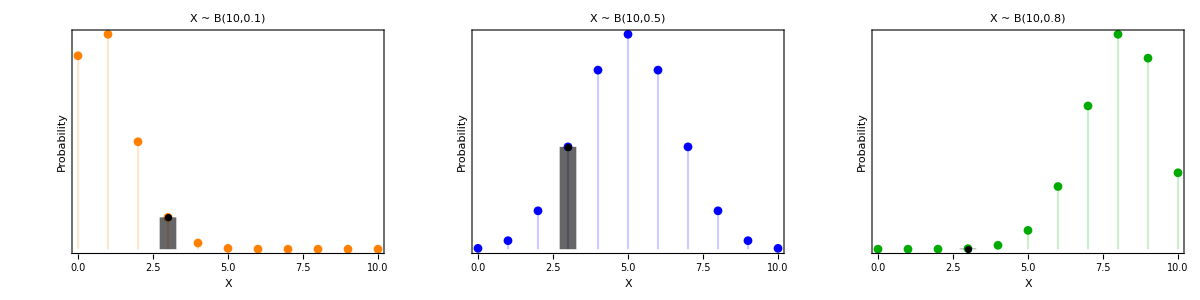

```mathematica
gFinal=Grid[{{g1,g2,g3}}]
```

```mathematica
Export["binomial_many_worlds.pdf",gFinal]
```

binomial_many_worlds.pdf

## Likelihoods

```mathematica
Likelihood[BinomialDistribution[10,θ],{3}]
```

120 (1-θ)^7 θ^3

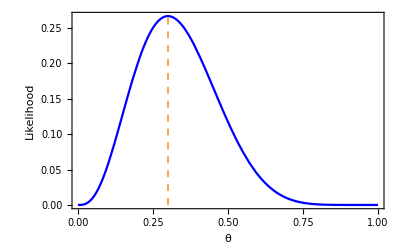

```mathematica
g=Plot[Likelihood[BinomialDistribution[10,θ],{3}],{θ,0,1},PlotStyle->Blue,Frame->{True,True,False,False},FrameLabel->{"θ","Likelihood"},LabelStyle->{Black,FontSize->16},FrameTicks->{True,None},Epilog->{Orange,Thick,Dashed,Line[{{0.3,0},{0.3,Likelihood[BinomialDistribution[10,0.3],{3}]}}]}]
```

```mathematica
Export["binomial_likelihood_eg.pdf",g]
```

binomial_likelihood_eg.pdf

```mathematica
int=NIntegrate[Likelihood[BinomialDistribution[10,θ],{3}],{θ,0,1}]
```

0.0909091

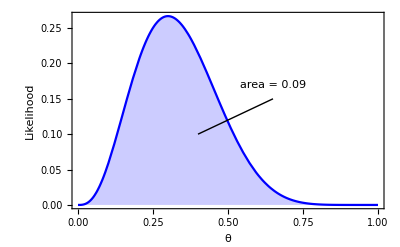

```mathematica
g=Plot[Likelihood[BinomialDistribution[10,θ],{3}],{θ,0,1},PlotStyle->Blue,Frame->{True,True,False,False},FrameLabel->{"θ","Likelihood"},LabelStyle->{Black,FontSize->16},FrameTicks->{True,True},Filling->Axis,Epilog->{Line[{{0.4,0.1},{0.65,0.15}}],Style[Text[StringJoin["area = 0.09"],{0.65,0.17}],16]}]
```

```mathematica
Export["binomial_likelihood_area.pdf",g]
```

binomial_likelihood_area.pdf

## Null hypothesis testing

```mathematica
Probability[x≤3,x\[Distributed]BinomialDistribution[10,0.5]]
```

0.171875

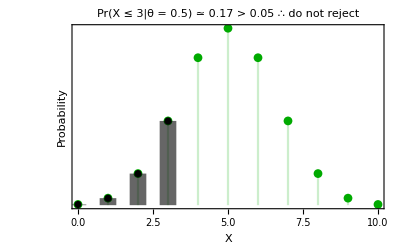

```mathematica
g=Show[DiscretePlot[PDF[BinomialDistribution[10,0.5],x],{x,0,10},PlotStyle->Darker[Green],Frame->{True,True,False,False},PlotMarkers->{Automatic, 9},FrameLabel->{"X","Probability"},LabelStyle->{Black,FontSize->16},FrameTicks->{True,None},
ImageSize->imagesize,PlotLabel->"Pr(X ≤ 3|θ = 0.5) ≃ 0.17 > 0.05 ∴ do not reject"],DiscretePlot[PDF[BinomialDistribution[10,0.5],x],{x,0,3},AspectRatio->1.5,Filling->Axis,PlotStyle->{Black},FillingStyle->Directive[{Thickness[0.03],Opacity[0.6,Black]}],PlotRange->{{0,25},{0,0.2}}]]
```

```mathematica
Export["binomial_h0_accept.pdf",g]
```

binomial_h0_accept.pdf

```mathematica
Probability[x≤3,x\[Distributed]BinomialDistribution[10,0.8]]
```

0.000864358

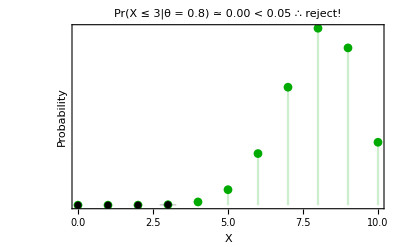

```mathematica
g=Show[DiscretePlot[PDF[BinomialDistribution[10,0.8],x],{x,0,10},PlotStyle->Darker[Green],Frame->{True,True,False,False},PlotMarkers->{Automatic, 9},FrameLabel->{"X","Probability"},LabelStyle->{Black,FontSize->16},FrameTicks->{True,None},
ImageSize->imagesize,PlotLabel->"Pr(X ≤ 3|θ = 0.8) ≃ 0.00 < 0.05 ∴ reject!"],DiscretePlot[PDF[BinomialDistribution[10,0.8],x],{x,0,3},AspectRatio->1.5,Filling->Axis,PlotStyle->{Black},FillingStyle->Directive[{Thickness[0.03],Opacity[0.6,Black]}],PlotRange->{{0,25},{0,0.2}}]]
```

```mathematica
Export["binomial_h0_reject.pdf",g]
```

binomial_h0_reject.pdf

```mathematica
NSolve[Probability[x≥3,x\[Distributed]BinomialDistribution[10,θ]]==0.05,θ]
```

{{θ→-0.040449-0.0565663 ⅈ},{θ→-0.040449+0.0565663 ⅈ},{θ→0.0872644},{θ→0.615493-0.526322 ⅈ},{θ→0.615493+0.526322 ⅈ},{θ→1.06785-0.588266 ⅈ},{θ→1.06785+0.588266 ⅈ},{θ→1.42329-0.375579 ⅈ},{θ→1.42329+0.375579 ⅈ},{θ→1.55815}}

```mathematica
Probability[x≥3,x\[Distributed]BinomialDistribution[10,0.087]]
```

0.0496182

## Bayesian inference

```mathematica
a=2;
b=8;
prior=PDF[BetaDistribution[a,b],θ];
like=10Likelihood[BinomialDistribution[10,θ],{3}];
post=PDF[BetaDistribution[a+3,b+10-3],θ];
```

```mathematica
cols={Blue,Orange,Black};
```

```mathematica
g3=Plot[{prior,like,post},{θ,0,1},PlotLegends->Placed[{"prior","likelihood (data)","posterior"},{0.75,0.5}],LabelStyle->{Black,FontSize->16},Frame->{True,True,False,False},FrameLabel->{"θ, disease prevalence",None},PlotStyle->cols,FrameTicks->{Automatic,None},PlotRange->{Automatic,{0,4.4}}];
g2=Plot[{prior,like},{θ,0,1},PlotLegends->Placed[{"prior","likelihood (data)"},{0.75,0.5}],LabelStyle->{Black,FontSize->16},Frame->{True,True,False,False},FrameLabel->{"θ, disease prevalence",None},PlotStyle->cols,FrameTicks->{Automatic,None},PlotRange->{Automatic,{0,4.4}}];
g1=Plot[{prior},{θ,0,1},PlotLegends->Placed[{"prior"},{0.75,0.5}],LabelStyle->{Black,FontSize->16},Frame->{True,True,False,False},FrameLabel->{"θ, disease prevalence",None},PlotStyle->cols[[1]],FrameTicks->{Automatic,None},PlotRange->{Automatic,{0,4.4}}];
```

```mathematica
Export["binomial_prior.pdf",g1]
Export["binomial_likelihood.pdf",g2]
Export["binomial_posterior.pdf",g3]
```

binomial_prior.pdf

binomial_likelihood.pdf

binomial_posterior.pdf

## Credible intervals

```mathematica
lower=Quantile[BetaDistribution[a+3,b+10-3],0.05];
upper=Quantile[BetaDistribution[a+3,b+10-3],0.95];
```

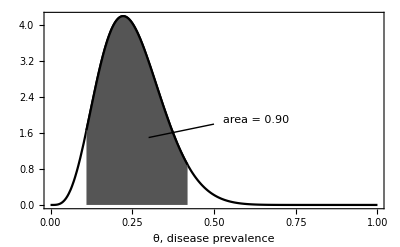

```mathematica
g=Show[Plot[post,{θ,0,1},LabelStyle->{Black,FontSize->16},Frame->{True,True,False,False},FrameLabel->{"θ, disease prevalence",None},PlotStyle->cols[[3]],Epilog->{Line[{{0.3,1.5},{0.5,1.8}}],Style[Text[StringJoin["area = 0.90"],{0.63,1.9}],16]}],Plot[post,{θ,lower,upper},LabelStyle->{Black,FontSize->16},Frame->{True,True,False,False},FrameLabel->{"θ, disease prevalence",None},PlotStyle->cols[[3]],Filling->Bottom,FillingStyle->Darker[Gray],PlotRange->{Automatic,{0,Automatic}}]]
```

```mathematica
Export["binomial_credible_interval.pdf",g]
```

binomial_credible_interval.pdf

```mathematica
lower
```

0.109906

```mathematica
upper
```

0.41912

## Animations

```mathematica
options4={Frame->{True,True,False,False},FrameStyle->Black,BaseStyle->{FontSize->16},LabelStyle->{Black,FontSize->16}};
aAxisLabel="θ, disease prevalence";
aUpper = 10;
aPDNumber =3;
```

```mathematica
fPlotAll[a_,b_,n_Integer,numPD_Integer,aAspectRatio_]:=Module[{g1=Plot[PDF[BetaDistribution[a,b],x],{x,0,1},PlotRange->Full,Evaluate@options4,FrameTicks->{Automatic,None},FrameLabel->{None,"density"},PlotStyle->{Thickness[0.005],Blue},PlotLabel->"prior",AspectRatio->aAspectRatio],
g2=Plot[Likelihood[BinomialDistribution[n,θ],{numPD}],{θ,0,1},PlotRange->Full,PlotStyle->{Thickness[0.005],Orange},Evaluate@options4,FrameTicks->{Automatic,None},FrameLabel->{None,"likelihood "},PlotLabel->"likelihood",AspectRatio->aAspectRatio],
g3=Plot[PDF[BetaDistribution[a+numPD,b+n-numPD],θ],{θ,0,1},PlotRange->Full,PlotStyle->{Thickness[0.005],Darker[Green]},Evaluate@options4,FrameTicks->{Automatic,None},FrameLabel->{aAxisLabel,"density"},PlotLabel->"posterior",AspectRatio->aAspectRatio]},gFinal=Column[Show[#,ImageSize->800]&/@{g1,g2,g3}]]
```

```mathematica
gTest=Table[If[i==1,fPlotAll[i,1,aUpper,aPDNumber,0.15],fPlotAll[i,3,10,aPDNumber,0.15]],{i,1,10,0.25}];
```

```mathematica
gTest1=Table[fPlotAll[2,8,aUpper,i,0.15],{i,0,10,1}];
```

```mathematica
gTest2=Table[fPlotAll[2,8,n,Round[0.3 n],0.15],{n,10,400,20}];
```

General::munfl: 4.84719×10^-308 0.05 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-712.694] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-765.304] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
Table[Export[StringJoin["../animations/binomial_prior_",ToString@i,".pdf"],gTest[[i]]],{i,1,Length@gTest,1}];
Table[Export[StringJoin["../animations/binomial_likelihood_",ToString@i,".pdf"],gTest1[[i]]],{i,1,Length@gTest1,1}];
Table[Export[StringJoin["../animations/binomial_posterior_",ToString@i,".pdf"],gTest2[[i]]],{i,1,Length@gTest2,1}];
```

## Denominator example

```mathematica
PlotAll1[a_,b_,n_Integer,numPD_Integer,aAspectRatio_]:=Module[{g1=Plot[PDF[BetaDistribution[a,b],x],{x,0,1},PlotRange->Full,Evaluate@options4,FrameTicks->{Automatic,None},FrameLabel->{None,"density"},PlotStyle->{Thickness[0.005],Blue},PlotLabel->"prior",AspectRatio->aAspectRatio],
g2=Plot[Likelihood[BinomialDistribution[n,θ],{numPD}],{θ,0,1},PlotRange->Full,PlotStyle->{Thickness[0.005],Orange},Evaluate@options4,FrameTicks->{Automatic,None},FrameLabel->{None,"likelihood "},PlotLabel->"likelihood",AspectRatio->aAspectRatio],
g3=Plot[PDF[BetaDistribution[a+numPD,b+n-numPD],θ],{θ,0,1},PlotRange->Full,PlotStyle->{Thickness[0.005],Darker[Green]},Evaluate@options4,FrameTicks->{Automatic,None},FrameLabel->{aAxisLabel,""},PlotLabel->"likelihood x prior",AspectRatio->aAspectRatio]},gFinal=Column[Show[#,ImageSize->800]&/@{g1,g2,g3}]]
PlotAll2[a_,b_,n_Integer,numPD_Integer,aAspectRatio_]:=Module[{g1=Plot[PDF[BetaDistribution[a,b],x],{x,0,1},PlotRange->Full,Evaluate@options4,FrameTicks->{Automatic,None},FrameLabel->{None,"density"},PlotStyle->{Thickness[0.005],Blue},PlotLabel->"prior",AspectRatio->aAspectRatio],
g2=Plot[Likelihood[BinomialDistribution[n,θ],{numPD}],{θ,0,1},PlotRange->Full,PlotStyle->{Thickness[0.005],Orange},Evaluate@options4,FrameTicks->{Automatic,None},FrameLabel->{None,"likelihood "},PlotLabel->"likelihood",AspectRatio->aAspectRatio],
g3=Plot[PDF[BetaDistribution[a+numPD,b+n-numPD],θ],{θ,0,1},PlotRange->Full,PlotStyle->{Thickness[0.005],Darker[Green]},Evaluate@options4,FrameTicks->{Automatic,None},FrameLabel->{aAxisLabel,""},PlotLabel->"likelihood x prior",AspectRatio->aAspectRatio,Filling->Axis,FillingStyle->Darker[Green],Epilog->{Style[Text["Pr(X = 3) ≃ 0.15",{0.75,2}],FontSize->22],Line[{{0.3,1},{0.63,2}}]}]},gFinal=Column[Show[#,ImageSize->800]&/@{g1,g2,g3}]]
```

```mathematica
g1=PlotAll1[2,8,aUpper,3,0.15];
g2=PlotAll2[2,8,aUpper,3,0.15];
```

```mathematica
Export["binomial_area_1.pdf",g1]
Export["binomial_area_2.pdf",g2]
```

binomial_area_1.pdf

binomial_area_2.pdf

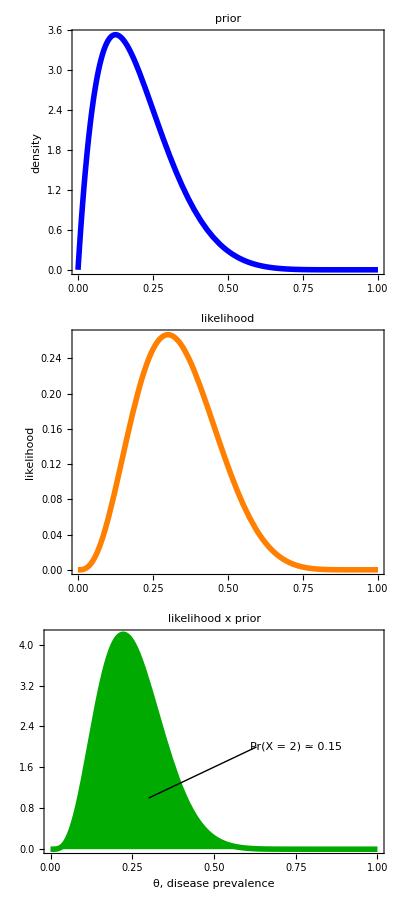

```mathematica
PlotAll2[2,8,aUpper,3,0.15]
```

```mathematica
a=2;
b=8;
prior=PDF[BetaDistribution[a,b],θ];
like=Likelihood[BinomialDistribution[10,θ],{3}];
```

```mathematica
NIntegrate[prior like, {θ,0,1}]
```

0.148607